## Import dati

```mathematica
Clear[a,b,c];
a=Import[NotebookDirectory[]<>"meas_noPerm_plus_chi8.dat"];
b=Import[NotebookDirectory[]<>"meas_Ref_plus_chi8.dat"];
(*c=Import[NotebookDirectory[]<>"meas_vecRho_qtech.dat"];*)
```

```mathematica
a[[1]]
```

{#,time,N_11,N_21,N_31,N_41,N_51,N_61,N_71,N_81,N_82,N_83,N_84,N_85,N_86,N_87,Sx_1,Sz_1,re_over,im_over,Norm}

```mathematica
b[[1]]
```

{#,time,N_11,N_21,N_31,N_41,N_51,N_61,N_71,N_81,N_82,N_83,N_84,N_85,N_86,N_87,Sx_1,Sz_1,re_over,im_over,Norm}

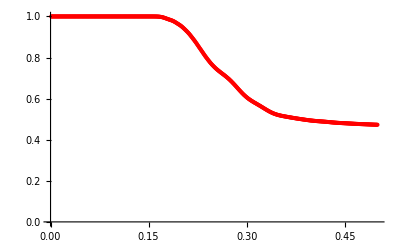

```mathematica
Clear[normMCEff];
normMCEff = ListPlot[Transpose[{Drop[a[[All,1]],1],Drop[a[[All,-1]],1]^2}] ,PlotStyle->Red]
```

## ⟨σx⟩

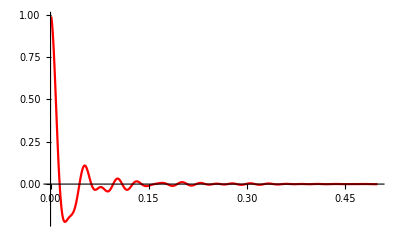

```mathematica
sx = ListPlot[Transpose[{Drop[a[[All,1]],1],2(Drop[a[[All,-5]],1])(*/Drop[a[[All,-1]],1]^2*)}],PlotStyle->Red,PlotRange->All,Joined->True]
```

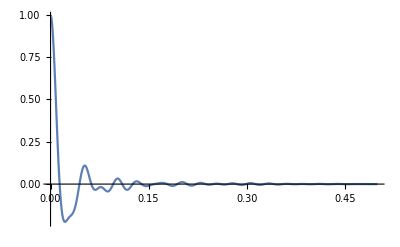

```mathematica
sxRef = ListPlot[Transpose[{b[[All,1]],2 b[[All,-5]]}],PlotRange->All,Joined->True]
```

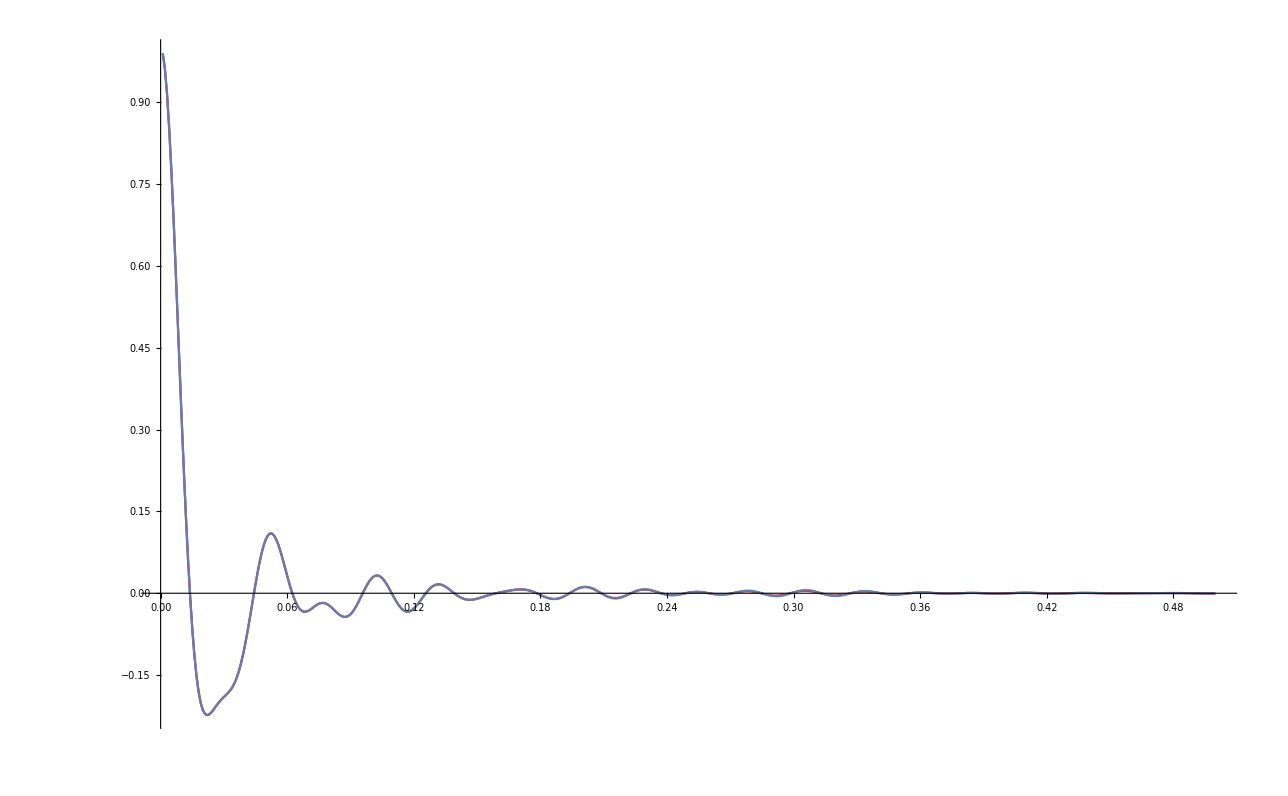

```mathematica
Show[sx,sxRef,PlotRange->All]
```

## ⟨N_11⟩

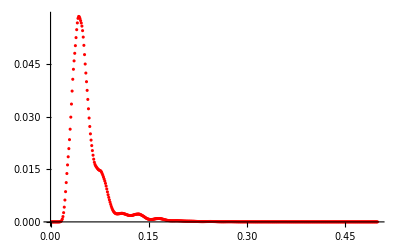

```mathematica
Clear[n11];
n11 = ListPlot[Transpose[{Drop[a[[All,1]],1],Drop[a[[All,2]],1](*/Drop[a[[All,-1]],1]^2*)}],PlotStyle->Red,PlotRange->All]
```

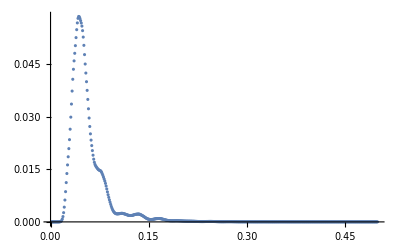

```mathematica
Clear[n11Ref];
n11Ref = ListPlot[Transpose[{b[[All,1]], b[[All,2]]}],PlotRange->All]
```

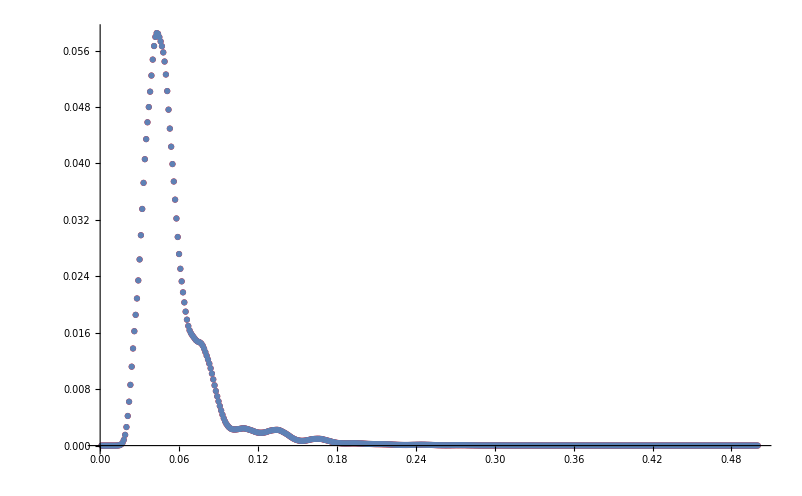

```mathematica
Show[n11,n11Ref,PlotRange->All]
```

## ⟨N_41⟩

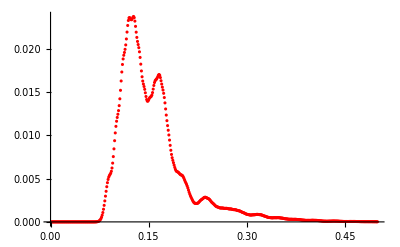

```mathematica
Clear[n41];
n41 = ListPlot[Transpose[{Drop[a[[All,1]],1],Drop[a[[All,5]],1](*/Drop[a[[All,-1]],1]^2*)}],PlotStyle->Red,PlotRange->All]
```

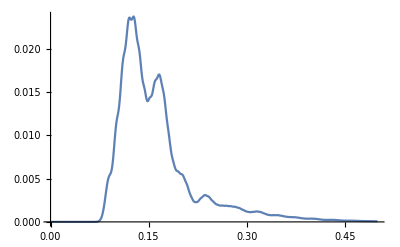

```mathematica
Clear[n41Ref];
n41Ref = ListPlot[Transpose[{b[[All,1]], b[[All,5]]}],PlotRange->All,Joined->True]
```

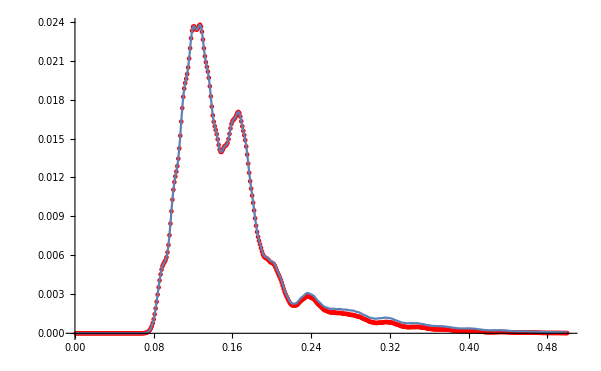

```mathematica
Show[n41,n41Ref,PlotRange->All]
```

## ⟨N_81⟩

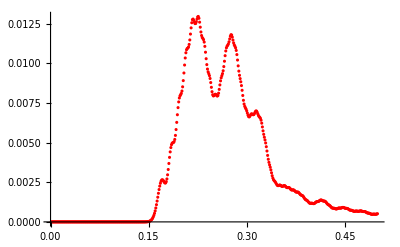

```mathematica
Clear[n81];
n81 = ListPlot[Transpose[{Drop[a[[All,1]],1],Drop[a[[All,9]],1](*/Drop[a[[All,-1]],1]^2*)}],PlotStyle->Red,PlotRange->All]
```

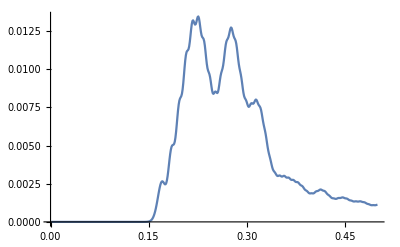

```mathematica
Clear[n81Ref];
n81Ref = ListPlot[Transpose[{b[[All,1]], b[[All,9]]}],PlotRange->All,Joined->True]
```

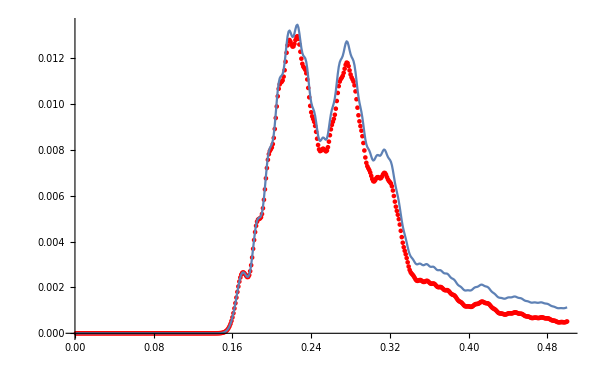

```mathematica
Show[n81,n81Ref,PlotRange->All]
```